# 2 D square lattice with s & px, py, pz AO

Angel Salazar	
School of Physical Sciences and Nanotechnology

We are going to compute the electronic bnad structure of a 2D crystal with 1 atoms per unit cell (UC) and  s, px, py , and  pz atomic orbitals AO

-Graphics-

Let's define the matrix elements of the associated Hamiltonian that has a rank of 4x4; but we know that for this case there are only 6 independent elements.

```mathematica
h[1,1]=es +2 tss (Cos[kx a]+Cos[ky a]);
h[2,2]=ep + 2 tppσ (Cos[kx a])+ 2 tppπ (Cos[ky a]);
h[3,3]=ep + 2 tppπ (Cos[kx a])+ 2 tppσ (Cos[ky a]);
h[4,4]=ep +2 tppπ (Cos[kx a]+Cos[ky a]);
h[1,2]=-2 ⅈ tsp Sin[kx a];
h[1,3]=-2 ⅈ tsp Sin[ky a];
h[2,1]=2 ⅈ tsp Sin[kx a];
h[3,1]=2 ⅈ tsp Sin[ky a];
h[1,4]=h[4,1]=0;
h[2,3]=h[3,2]=0;
h[2,4]=h[4,2]=0;
h[3,4]=h[4,3]=0;
```

Now we define the Hamiltonian

```mathematica
H=Table[h[i,j],{i,4},{j,4}];
H//MatrixForm
```

(es+2 tss (Cos[a kx]+Cos[a ky]) | -2 ⅈ tsp Sin[a kx] | -2 ⅈ tsp Sin[a ky] | 0
2 ⅈ tsp Sin[a kx] | ep+2 tppσ Cos[a kx]+2 tppπ Cos[a ky] | 0 | 0
2 ⅈ tsp Sin[a ky] | 0 | ep+2 tppπ Cos[a kx]+2 tppσ Cos[a ky] | 0
0 | 0 | 0 | ep+2 tppπ (Cos[a kx]+Cos[a ky]))

```mathematica
eigenv=(Eigenvalues[H]//FullSimplify)//PowerExpand;
```

```mathematica
Dimensions[eigenv]
```

{4}

```mathematica
eigenv[[1]]
```

ep+2 tppπ (Cos[a kx]+Cos[a ky])

Let’s plot the eigenvalues within the BZ, in fact they are surfaces

```mathematica
Plot3D[Table[eigenv[[i]],{i,4}]/.{es->-8,ep->0,tss->-2,tppσ->2.2,tppπ->-1.8,tsp->-2.1,a->π}//Evaluate,{kx,-1,1},{ky,-1,1},
PlotPoints->30,
MaxRecursion->0,
AxesLabel->{"k_x","k_y","k_z"},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
BoxRatios->{1,1,1.3},
ViewPoint->{0,0,∞}
]
```

-Graphics3D-

With the following restriction we can get the reducible broullin zone

```mathematica
Plot3D[Table[eigenv[[i]],{i,4}]/.{es->-8,ep->0,tss->-2,tppσ->2.2,tppπ->-1.8,tsp->-2.1,a->π}//Evaluate,{kx,-1,1},{ky,-1,1},
PlotPoints->30,
MaxRecursion->0,
AxesLabel->{"k_x","k_y","k_z"},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
BoxRatios->{1,1,1.3},
ViewPoint->{0,0,∞},
RegionFunction->Function[{x,y,z},y<x]
]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[Table[eigenv[[i]],{i,4}]/.{es->esv,ep->0,tss->tssv,tppσ->tppσv,tppπ->tppπv,tsp->tspv,a->π}//Evaluate,{kx,-1,1},{ky,-1,1},
PlotPoints->30,
MaxRecursion->0,
AxesLabel->{"k_x","k_y","k_z"},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
BoxRatios->{1,1,1.3},
ViewPoint->{0,0,∞},
RegionFunction->Function[{x,y,z},y<x&&y≥0]
],
{{esv,-8,"ϵ_s"},-16,0},
{{tssv,-2,"t_ss"},-4,-1},
{{tppσv,2,"t_ppσ"},0,5},
{{tppπv,-1.8,"t_ppπ"},-4,1.5},
{{tspv,-2.1,"t_ps"},-4.5,-1},ControlPlacement->Right
]
```

Changing tss we notice that the more parabolic the more change of tunneling, overlap between the orbitals.
Tppsigma, we see that is afecting the red band and green band. Changing the tpppi we affect all the bands. Tps affects the blue and the red bands.  In parabolic dispersion, the electrons moves as free electron, but if the bans are flat, the electron is full localized. The higher dispersion the electrons are free to move.

What are the reciprocal lattice vector of this 2 D lattice .

```mathematica
a1=a{1,0,0};
a2=a{0,1,0};
a3={0,0,b};
b1=2 π (a2 × a3)/(a1.(a2 ×a3))
b2=2 π (a3 × a1)/(a1.(a2 ×a3))
b3=2 π (a1 × a2)/(a1.(a2 ×a3))
```

{(2 π)/a,0,0}

{0,(2 π)/a,0}

{0,0,(2 π)/b}

Let’s compute the Band structure along the high symmetry point: X-Γ-M-X

```mathematica
-Graphics--Graphics-
```

-Graphics- -Graphics-

We plot the first eigenvalue

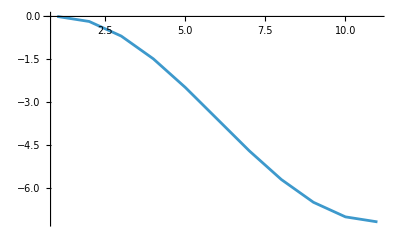

```mathematica
i=1;
XΓ[i]=Table[eigenv[[i]]/.{es->-8,ep->0,tss->-2,tppσ->2.2,tppπ->-1.8,tsp->-2.1,a->π,ky->0},{kx,1},{kx,1,0,-0.1}];
XΓ[i]//ListPlot[#,Joined->True,PlotRange->All]&
```

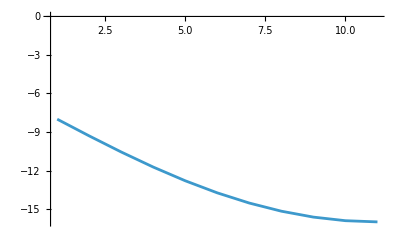

```mathematica
i=2;
XΓ[i]=Table[eigenv[[i]]/.{es->-8,ep->0,tss->-2,tppσ->2.2,tppπ->-1.8,tsp->-2.1,a->π,ky->0},{kx,1},{kx,1,0,-0.1}];
XΓ[i]//ListPlot[#,Joined->True,PlotRange->All]&
```

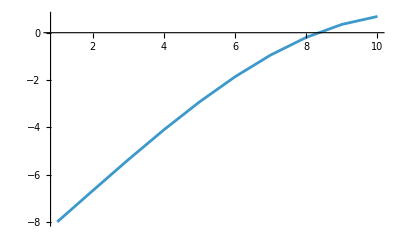

```mathematica
i=3;
XΓ[i]=Table[eigenv[[i]]/.{es->-8,ep->0,tss->-2,tppσ->2.2,tppπ->-1.8,tsp->-2.1,a->π,ky->0},{kx,1},{kx,1,0,-0.1}];
XΓ[i]//ListPlot[#,Joined->True,PlotRange->All]&
```

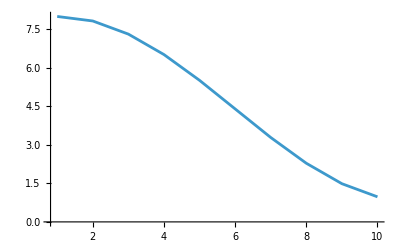

```mathematica
i=4;
XΓ[i]=Table[eigenv[[i]]/.{es->-8,ep->0,tss->-2,tppσ->2.2,tppπ->-1.8,tsp->-2.1,a->π,ky->0},{kx,1},{kx,1,0,-0.1}];
XΓ[i]//ListPlot[#,Joined->True,PlotRange->All]&
```

#### Bands-1

```mathematica
Table[XΓ[i]=Table[eigenv[[i]]/.{es->-8,ep->0,tss->-2,tppσ->2.2,tppπ->-1.8,tsp->-2.1,a->π,ky->0},{kx,0.9999,0,-0.02}],{i,4}];
```

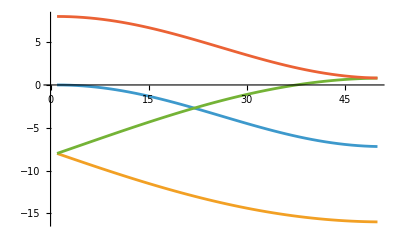

```mathematica
pathXΓ=ListPlot[Table[XΓ[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+0.,#1}&,#]&, {i,4}],Joined->True,PlotRange->All]
```

```mathematica
Table[ΓM[i]=Table[eigenv[[i]]/.
{es->-8,
ep->0,
tss->-2,tppσ->2.2,
tppπ->-1.8,
tsp->-2.1,
a->π,
ky->kx


},{kx,0,0.999,0.02}

],{i,4}];
```

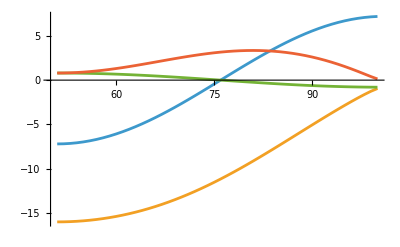

```mathematica
pathΓM=ListPlot[Table[ΓM[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+50,#1}&,#]&, {i,4}],Joined->True,PlotRange->All]
```

```mathematica
Table[MX[i]=Table[eigenv[[i]]/.
{es->-8,
ep->0,
tss->-2,tppσ->2.2,
tppπ->-1.8,
tsp->-2.1,
a->π,
kx->1


},{ky,0.999,0,-0.02}

],{i,4}];
```

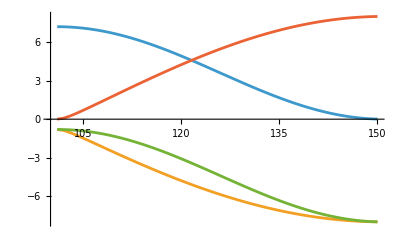

```mathematica
pathMX=ListPlot[Table[MX[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+100,#1}&,#]&, {i,4}],Joined->True,PlotRange->All]
```

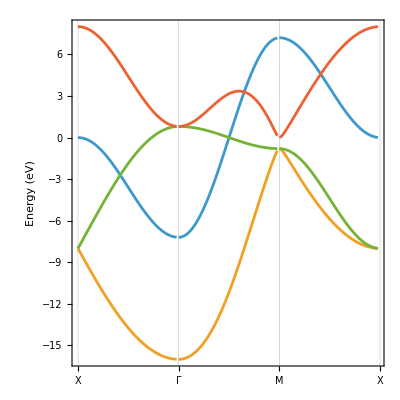

```mathematica
gridline=Range[1,151,50];
hsplabel={"X","Γ","M","X"};
Show[pathXΓ,pathΓM,pathMX,
PlotRange->All,
Frame->True,
FrameLabel->{"","Energy (eV)"},
Axis->None,
AspectRatio->1,
GridLines->{gridline,None},
FrameTicks->{{Automatic,None},{{gridline,hsplabel}//Transpose,None}},
BaseStyle->{FontFamily->"Helvetica",FontSize->15}
]
```

Challenge

#### Bands-2

```mathematica
Table[XΓ[i]=Table[eigenv[[i]]/.{es->-16,ep->0,tss->-2,tppσ->2.2,tppπ->-1.8,tsp->-2.1,a->π,ky->0},{kx,0.9999,0,-0.02}],{i,4}];
```

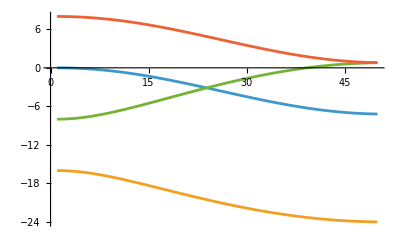

```mathematica
pathXΓ=ListPlot[Table[XΓ[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+0.,#1}&,#]&, {i,4}],Joined->True,PlotRange->All]
```

```mathematica
Table[ΓM[i]=Table[eigenv[[i]]/.
{es->-16,
ep->0,
tss->-2,tppσ->2.2,
tppπ->-1.8,
tsp->-2.1,
a->π,
ky->kx


},{kx,0,0.999,0.02}

],{i,4}];
```

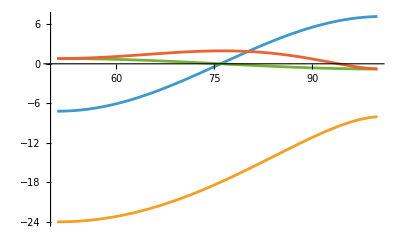

```mathematica
pathΓM=ListPlot[Table[ΓM[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+50,#1}&,#]&, {i,4}],Joined->True,PlotRange->All]
```

```mathematica
Table[MX[i]=Table[eigenv[[i]]/.
{es->-16,
ep->0,
tss->-2,tppσ->2.2,
tppπ->-1.8,
tsp->-2.1,
a->π,
kx->1


},{ky,0.999,0,-0.02}

],{i,4}];
```

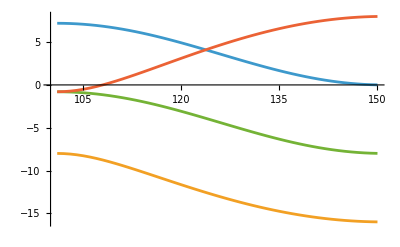

```mathematica
pathMX=ListPlot[Table[MX[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+100,#1}&,#]&, {i,4}],Joined->True,PlotRange->All]
```

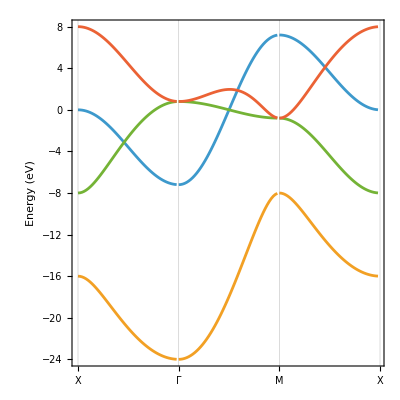

```mathematica
gridline=Range[1,151,50];
hsplabel={"X","Γ","M","X"};
Show[pathXΓ,pathΓM,pathMX,
PlotRange->All,
Frame->True,
FrameLabel->{"","Energy (eV)"},
Axis->None,
AspectRatio->1,
GridLines->{gridline,None},
FrameTicks->{{Automatic,None},{{gridline,hsplabel}//Transpose,None}},
BaseStyle->{FontFamily->"Helvetica",FontSize->15}
]
```

Challenge

## Effect of the lattice parameter on the band structure

Let' s explore the effect of the change of the unit cell on the band structure . To model this, we will do an approximation of exponential decay as first approximation on the hopping parameters t.  Here we will assume that a0=3 Å for the optimal parameter.

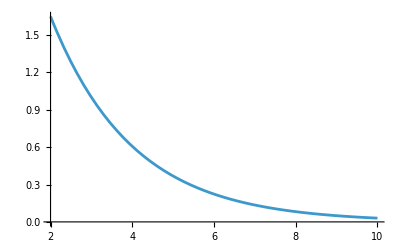

```mathematica
a0=3;
Plot[Exp[(a0-a)/2],{a,2,10}]
```

```mathematica
a0=3;
Manipulate[Plot3D[Table[eigenv[[i]],{i,4}]/.{es->esv,ep->0,tss ->tssv Exp[(a0-av)/2],tppσ->tppσv Exp[(a0-av)/2],tppπ->tppπv Exp[(a0-av)/2],tsp->tspv Exp[(a0-av)/2],a->av}//Evaluate,{kx,0,π/av},{ky,0,π/av},
PlotPoints->30,
MaxRecursion->0,
AxesLabel->{"k_x","k_y","k_z"},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
BoxRatios->{1,1,1.3},
ViewPoint->{0,0,∞},
RegionFunction->Function[{x,y,z},y<x&&y≥0],
PlotRange->{{0,π},{0,π},{-30,22}}
],
{{av,3,"a"},1,10},
{{esv,-8,"ϵ_s"},-16,0},
{{tssv,-2,"t_ss"},-4,-1},
{{tppσv,2,"t_ppσ"},0,5},
{{tppπv,-1.8,"t_ppπ"},-4,1.5},
{{tspv,-2.1,"t_ps"},-4.5,-1},ControlPlacement->Right
]
```